# Fuzzy Sphere

```mathematica
<<BProbeM` (* load the package BProbe *)
```

Loaded BProbeM. See the  for help.

The quantized embedding functions of the fuzzy sphere (S^2)_n are given by the N-dimensional SU(2) representation:

```mathematica
n = 10; (* in this example n=10 *)
t=2/Sqrt[n^2-1]MatrixRepSU2[n];
```

## Laplacian Point Probe

### Initialize the probe

```mathematica
ProbeInit[t]
```

Energy Probe | Laplace
Starting Point (SP) | (0.080153
-0.585913
0.684444)
Energy at SP | 0.181818
Norm of Gradient at SP | 0.000000556833
Absolute Hessian Eigenvalues at SP | (0.000110744
0.000235824
1.99976)
Local brane dimension at SP | 2
Dimension of Target Space | 3
Dimension of Hilbert Space | 10
Step size guess | 0.125434

### Start the scan with default values

```mathematica
ProbeScan[StepSize->0.3,EnergyTracker->True,EVTracker->True,GradientTracker->True]
```

Number of total points gathered | 602
Number of points currently processing | 0Status Information
Largest emerged Gradient norm | 0.000000732972
Smallest/Largest emerged Displacement Energy | [ 0.181818 , 0.181818 ]
Largest emerged 'small' Eigenvalue | 0.00219517Tracker

### Retrieving results ...

```mathematica
(* point cloud *)
pc = ProbeGetPoints[];
```

```mathematica
(* tangent spaces *)
ts = ProbeGetTangentspaces[];
```

```mathematica
(* generalized coherent states *)
cs = ProbeGetGroundstates[];
```

### ... and visualize it

#### Plain point cloud plot

```mathematica
ListPointPlot3D[pc, BoxRatios->Automatic]
```

#### Plot normals representing the tangent space

```mathematica
(* calculate normal to the surface *)
normals = Cross[#[[1]],#[[2]]]&/@ts;

(* orient and scale them in a uniform manner *)
normals = (normals[[#]]*0.3*Sign[normals[[#]][[1]]*pc[[#]][[1]]])&/@Range[1,Length[normals]];

(* and draw them as arrows *)
arrows = (Arrow[{pc[[#]],pc[[#]]+normals[[#]]}])&/@Range[1,Length[normals]];
Graphics3D[{Arrowheads[Small],arrows}]
```

### Or one might only want to consider a section through the x-z-plane

```mathematica
ProbeInit[t,Subspace->{1,3}]
```

Energy Probe | Laplace
Starting Point (SP) | (-0.903809
-0.0362002)
Energy at SP | 0.181818
Norm of Gradient at SP | 0.0000000480937
Absolute Hessian Eigenvalues at SP | (0.000242016
2.)
Local brane dimension at SP | 1
Dimension of Target Space | 2
Dimension of Hilbert Space | 10
Step size guess | 0.0330289

```mathematica
ProbeScan[StepSize->0.1]
```

Number of total points gathered | 57
Number of points currently processing | 0Status Information

```mathematica
pc=ProbeGetPoints[];
normals={#[[1,2]],-#[[1,1]]}&/@ProbeGetTangentspaces[];
normals=0.2*Sign[pc[[#]][[1]]*normals[[#]][[1]]]normals[[#]]&/@Range[1,Length[normals]];
arrows = (Arrow[{pc[[#]],pc[[#]]+normals[[#]]}])&/@Range[1,Length[normals]];
```

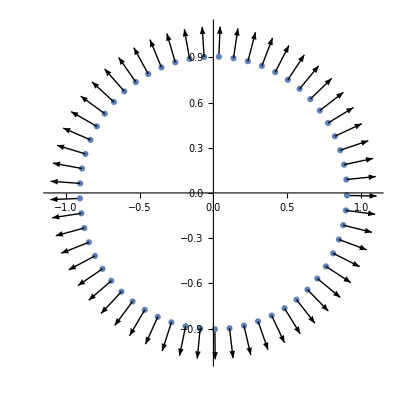

```mathematica
(* show generated point cloud with their normal vectors *)
Show[
ListPlot[pc,AspectRatio->Automatic],
Graphics[arrows]
, PlotRange->Automatic
]
```

## Dirac Point Probe

In the case of the fuzzy sphere the Dirac probe has exact zero modes, but generates equivalent results as you can convince you yourself.

### Initialize the probe

```mathematica
ProbeInit[t,Probe->"DiracSq"]
```

Energy Probe | DiracSq
Starting Point (SP) | (0.0801523
-0.585913
0.684444)
Energy at SP | 0.00000000000000000901741
Norm of Gradient at SP | 0.00000058841
Absolute Hessian Eigenvalues at SP | (0.000110709
0.00023586
1.99976)
Local brane dimension at SP | 2
Dimension of Target Space | 3
Dimension of Hilbert Space | 20
Step size guess | 0.125434

```mathematica
ProbeScan[EnergyTracker->True,EVTracker->True,GradientTracker->True]
```

Number of total points gathered | 3589
Number of points currently processing | 0Status Information
Largest emerged Gradient norm | 0.000000736871
Smallest/Largest emerged Displacement Energy | [ 0. , 0.00000000000000333368 ]
Largest emerged 'small' Eigenvalue | 0.000384452Tracker

```mathematica
ListPointPlot3D[ProbeGetPoints[],BoxRatios->Automatic]
```

-Graphics3D-